## Example 7.1

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
<<VariationalMethods`
```

```mathematica
EulerEquations[ Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
soln=DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,y[x],x];
```

```mathematica
y[x]/.soln
```

{C[1]+x C[2]}

## Example 7.2

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[ParametricPlot,Frame->True,Axes->False,BaseStyle->{FontSize->16}];
```

```mathematica
a=2;
```

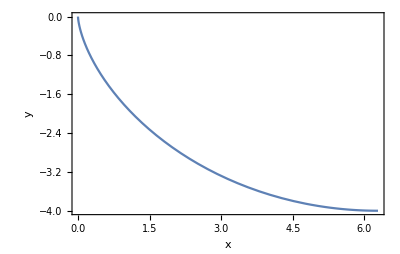

```mathematica
ParametricPlot[{a(θ-Sin[θ]),-a(1-Cos[θ])},{θ,0,π},FrameLabel->{"x","y"}]
```

## Example 7.4

```mathematica
Remove["Global`*"]
```

```mathematica
params=NSolve[a Cosh[1/a]==3,a,Reals]
```

{{a→0.353638},{a→2.82089}}

```mathematica
RevolutionPlot3D[a Cosh[z/a]/.params[[2]],{z,-1,1},RevolutionAxis->{1, 0, 0},ViewPoint->{1.3, -2.4, 2.},AxesLabel->{"x","y","z"},BaseStyle->{Black,Bold,FontSize->18}]
```

-Graphics3D-